Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Shortest spanning trees. Prim’s algorithm.

1.  When will S = E at the end of Prim’s algorithm?

3.  What is the result of applying Prim’s algorithm to a graph that is not connected?

6 - 13 Find a shortest spanning tree by Prim’s algorithm.

7.  Problem represented by a diagram.

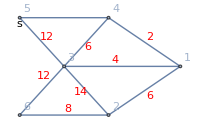

```mathematica
g1=Graph[{5<->4,4<->1,1<->2,2<->6,6<->3,3<->5,3<->1,3<->2,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{2.6,0},{4.7,-1.5},{2.6,-3},{0,-3},{1.3,-1.5}},EdgeWeight->{20,2,6,8,12,12,4,14,6},Epilog->{{Text[Style["s",Medium],{0,-0.2}]},{Red,Text[Style["6",Medium],{3.8,-2.4}]},{Red,Text[Style["14",Medium],{1.8,-2.3}]},{Red,Text[Style["12",Medium],{0.7,-1.8}]},{Red,Text[Style["4",Medium],{2.8,-1.3}]},{Red,Text[Style["8",Medium],{1.4,-2.8}]},{Red,Text[Style["12",Medium],{0.8,-0.6}]},{Red,Text[Style["20",Medium],{1.4,0.2}]},{Red,Text[Style["2",Medium],{3.8,-0.6}]},{Red,Text[Style["6",Medium],{2,-0.9}]}},ImageSize->200,ImagePadding->10]
```

```mathematica
FindSpanningTree[g1];
HighlightGraph[g1,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g1]]
```

32.

The highlighted graph above and the value in the green cell match the answer in the text.

7.  Problem represented by a diagram.

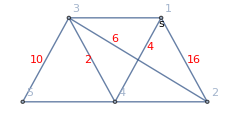

```mathematica
g5=Graph[{1<->2,1<->3,1<->4,3<->5,3<->4,4<->5,2<->4,2<->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,-2},{-2,0},{-1,-2},{-3,-2}},EdgeWeight->{16,8,4,10,2,14,4,6},Epilog->{{Text[Style["s",Medium],{0,-0.15}]},{Red,Text[Style["8",Medium],{-1,0.15}]},{Red,Text[Style["10",Medium],{-2.7,-1}]},{Red,Text[Style["6",Medium],{-1,-0.5}]},{Red,Text[Style["2",Medium],{-1.6,-1}]},{Red,Text[Style["14",Medium],{-2,-2.18}]},{Red,Text[Style["4",Medium],{0,-2.18}]},{Red,Text[Style["16",Medium],{0.7,-1}]},{Red,Text[Style["4",Medium],{-0.25,-0.7}]}},ImageSize->230,ImagePadding->10]
```

```mathematica
FindSpanningTree[g5];
HighlightGraph[g5,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g5]]
```

20.

The highlighted graph above and the value in green match the answer in the text.

11.  For the graph in problem 4, section 23.4.

The following graph is from problem 4 of the last section.

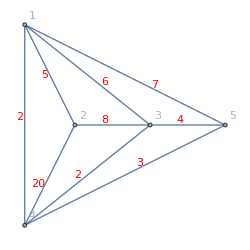

```mathematica
g4=Graph[{1<->2,2<->3,3<->5,1<->4,4<->2,1<->5,3<->4,4<->5,1<->3},VertexLabels->"Name",VertexCoordinates->{{0,2},{1,0},{2.5,0},{4,0},{0,-2}},EdgeWeight->{5,8,4,2,20,7,2,3,6},Epilog->{{Text[Style["s",Medium],{0-.14,1.85}]},{Red,Text[Style["2",Medium],{-0.1,0.15}]},{Red,Text[Style["5",Medium],{0.4,1}]},{Red,Text[Style["6",Medium],{1.6,0.85}]},{Red,Text[Style["7",Medium],{2.6,0.8}]},{Red,Text[Style["8",Medium],{1.6,0.1}]},{Red,Text[Style["20",Medium],{0.27,-1.18}]},{Red,Text[Style["2",Medium],{1.05,-1}]},{Red,Text[Style["3",Medium],{2.3,-0.75}]},{Red,Text[Style["4",Medium],{3.1,0.1}]}},ImageSize->250,ImagePadding->10]
```

```mathematica
FindSpanningTree[g4];
HighlightGraph[g4,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g4]]
```

12.

The highlighted graph above and the value in green match the answer in the text.